```mathematica
.3+.6*.7
```

0.72

```mathematica
.7*.4
```

0.28

```mathematica
7/8(.3)
```

```mathematica
0.2625*2+4
```

```mathematica
4.525
Clear[x, y, t, n, h]
```

4.525

```mathematica
f[x_]:=(1/Sqrt[Pi])Exp[-x^2]
```

```mathematica
(*We will estimate the integral on [0,1]*)

(*We will make our step size h=(4-0)/n*)

n=20
h=1/n
```

20

1/20

```mathematica
(*We now give the left endpoint rule*)
l = N[h Sum[f[h i], {i, 0, n-1}]]
```

0.43018

```mathematica
r = N[h Sum[f[h i], {i, 1, n}]]
```

0.412348

```mathematica
t = (r + l)/2
```

0.421264

```mathematica
(*The midpoint rule is given by*)
```

```mathematica
m = N[h Sum[f[h (i + .5)], {i, 0, n-1}]]
```

0.421394

```mathematica
t - m
```

-0.000129735

```mathematica
NIntegrate[f[t], {t, 0, 1}]
```

0.42135

```mathematica
Integrate[E^(-b^2), b]
```

```mathematica
1/2 √π Erf[b]
```

1/2 √π Erf[b]

```mathematica
(FunctionInterpolation[#1,{b,-12.,12.}]&)[1/2 √π Erf[b]]
```

InterpolatingFunction[…]

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{(√π)/2,{b→∞}}

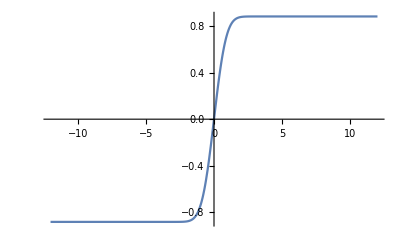

```mathematica
Plot[1/2 √π Erf[b],{b,-12.,12.}]
```

```mathematica
f[z_, i_] = Sin[z]*Cos[i]
```

Cos[i] Sin[z]

```mathematica
f[z, i^2]
```

```mathematica
Cos[i^2] Sin[z]

Plot3D[
```

```mathematica
Manipulate[Plot[Cos[i^2] Sin[z],{z,-2.7521183705382386,3.0787132514668505}],{i,-4.6947783604992335,2.8967823877683063}]
```